```mathematica
<<AtomicDensityMatrix`;
SetOptions[DensityMatrix,TimeDependence->False,ComplexExpandVariables->Subscript];
SetOptions[ListLinePlot,PlotRange->All,ImageSize->Medium,Frame->True];
{gstate,estate}=AtomicTransition["Cs","D2"];
{gQuantumNumbers,eQuantumNumbers}={AtomicData[gstate,{J,L,S,NuclearSpin,NaturalWidth,Energy}],
AtomicData[estate,{J,L,S,NuclearSpin}]};
system=Sublevels@{
AtomicState[1,gQuantumNumbers],AtomicState[2,Append[eQuantumNumbers,BranchingRatio[1]->1]]
};
Style[TableForm[system=DeleteStates[system,StateLabel==1&&F==3]],Small];
Style[TableForm[system=DeleteStates[system,StateLabel==2&&F==3]],Small];
Style[TableForm[system=DeleteStates[system,StateLabel==2&&F==4]],Small];
Style[TableForm[system=DeleteStates[system,StateLabel==2&&F==2]],
Small];
atomicData=Join[
AtomicData[gstate,StateLabel->1],
AtomicData[estate,StateLabel->2],{c->SpeedOfLight,ℏ->PlanckConstantReduced,ϵ0->VacuumPermittivity}
];
MatrixForm[h=Hamiltonian[system,ElectricField->OpticalField[ω,ΩR/ReducedME[1,{Dipole,1},2]]]];
(hrwa=RotatingWaveApproximation[system,h,ω]/.{ω->Energy[2]+Δ})//MatrixForm;
MatrixForm[relax=IntrinsicRelaxation[system]+TransitRelaxation[system,γ]];
MatrixForm[repop=OpticalRepopulation[system]+TransitRepopulation[system,γ]];
Short[eqs=Flatten@LiouvilleEquation[system,hrwa,relax,repop],25];
vars=DMVariables[system];
observables=Observables[system,Energy[2],ΩR/ReducedME[1,{Dipole,1},2]]//Together;
```

```mathematica
dADM=ExpandDipoleRME[system,ReducedME[1,{Dipole,1},2]];
dSI=Convert[dADM √(ℏ c^3)√(4 π ϵ0)/.atomicData,Coulomb Meter];
E0=Convert[√(2Int(Milli Watt/Centimeter^2)/(c ϵ0))/.atomicData//N,Volt/Meter];
rabi=ΩR->Convert[E0 dSI/ℏ/.atomicData,1/Second];

observables1=Convert[#,1]&/@(observables⟦All,1⟧ c^2 length (Centimeter) density(1/Centimeter^3)/.atomicData/.rabi);
Short[eqs1=eqs/.rabi/.atomicData/.{Mega->10^6,Second->1},50];
arrays[params_]:={
{1,-1}Reverse@CoefficientArrays[eqs1/.params,vars],CoefficientArrays[observables1/.params,vars]⟦2⟧
}
```

```mathematica
(*  LINEAR POLARIZATION *)
deltah=-3.757885799;
dlen=.1;
Powerinc=100 10^-6;
a=1.5 10^-3;
Intens=2Powerinc /(π a^2)/10
```

2.82942

```mathematica
(*  CIRCULAR POLARIZATION *)
```

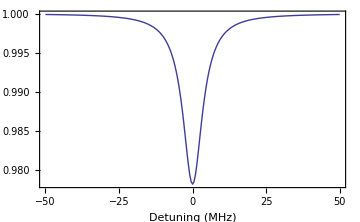

-255863.

```mathematica
params={Int->Intens (* mW/cm^2 *),γ->5 10^4 (* 1/s *),length->dlen(* cm *),density->1. 10^9 (* 1/cm^3 *),Δ->2π (deltah) 10^9 +2π (delta2) 10^6 (* GHz *)};
{eqarr,obsarr}=arrays[params];
tab=Table[{delta2,obsarr.LinearSolve@@eqarr},{delta2,-50,50,.5}];
ListLinePlot[{tab⟦All,2⟧[[All,1]]}+1,DataRange->tab⟦{1,-1},1⟧,FrameLabel->{"Detuning (MHz)"}]

abs=Total[tab⟦All,2⟧[[All,1]]]*.5 10^6
```

```mathematica
l
```

l

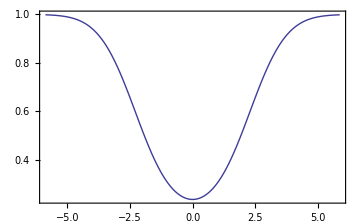

```mathematica
m=.133;R=8.314;T1=294;
σ=Sqrt[R T1/m];
v=Range[-500,500];
λ1=852 10^-9;
absorp=v 0;
For[k1=1,k1≤ Length[v],k1++,
absorp[[k1]]=abs*30*λ1/(Sqrt[2 π]σ) Exp[-v[[k1]]^2/σ^2/2];
]

length1 =7.5; (* Total length*)
finallin=Exp[absorp/dlen length1];

df=v/λ1;
ListLinePlot[Thread[{df,finallin}]]
```